{{x→-(-1)^(1/3)},{x→(-1)^(1/3)},{x→-(-1)^(2/3)},{x→(-1)^(2/3)}}

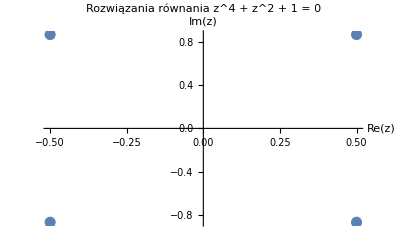

```mathematica
(* Rozwiązanie równania *)
solutions = Solve[x^4 + x^2 + 1 == 0, x]

(* Wyodrębnienie rzeczywistych i urojonych części rozwiązań *)
realSolutions = Re[x /. solutions];
imagSolutions = Im[x /. solutions];

(* Narysowanie rozwiązań na płaszczyźnie zespolonej *)
ListPlot[Transpose[{realSolutions, imagSolutions}], PlotStyle -> PointSize[0.02], AxesLabel -> {"Re(z)", "Im(z)"}, PlotLabel -> "Rozwiązania równania z^4 + z^2 + 1 = 0"]
```

```mathematica
Solve[z^6-1==0, z]
```

{{z→-1},{z→1},{z→-(-1)^(1/3)},{z→(-1)^(1/3)},{z→-(-1)^(2/3)},{z→(-1)^(2/3)}}

```mathematica
f[z_]=(z^2−1)*(z^4+z^2+1)
```

(-1+z^2) (1+z^2+z^4)

```mathematica
g[z_]=z^6-1
```

-1+z^6

```mathematica
Simplify[f[z]==g[z]]
```

True